# μLang — Computationally Generating a Morphologically Average Conlang using Multilingual Translations

Constructed languages, or conlangs, are languages that were artificially created instead of being naturally evolved over several generations. A crucial part of every conlang is the lexicon — the vocabulary. While most lexicons are generated manually or through the help of randomized selection, I present several methods to generating a quantitatively “average” lexicon, that is, generating new words that may have similar features, spelling, or pronunciation compared to several translations of the same word in different languages.

## Initial Setup

We start with a simple word and and using translations provided by the Wolfram Language. In this case, I’m using “language.”

```mathematica
KEYWORD = "river";
```

Generate translations of KEYWORD into many languages

```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation[KEYWORD, All]];
rawTranslations//Short
```

{Mandarin Chinese→河,Hindi→नदी,Spanish→río,Russian→река,Indonesian→sungai,Portuguese→rio,Bengali→নদী,Arabic→نَهر,Malay→sungai,Japanese→川,French→rivière,German→Fluss°,Urdu→دریا,Javanese→kali,Turkish→nehir,Telugu→నది,Marathi→नदी,Vietnamese→dòng sông,Korean→강,Tamil→ஆறு,Thai→แม่น้ำ,«139»,Romansch→flum,Evenki→бира,Chorti→xukur,Khanty→ас,Chukot→вээм,Sanskrit→नदी,Chiripá→ry,Nanai→махгбо,Choctaw→hatcha,Mansi→ас,Koryak→в'эем,Ho-Chunk→ní xáte,Karaim→чырпыкъ,Karon Dori→эҥер,Bai→kare,Batak→sunge,Gilyak→эри,Alabama→pahnichoba,Judeo-Crimean Tatar→чай,Latin→flumen,Classical Quechua→mayu}

Standardize all translated words — Transliterate to the Roman alphabet and ensure all words are lowercase

```mathematica
translatedList=DeleteDuplicates[ToLowerCase[Select[Transliterate[Values[rawTranslations]],StringMatchQ[#,CharacterRange["A","z"]..]&]]]
```

{he,nadi,rio,reka,sungai,nahr,chuan,riviere,drya,kali,nehir,gang,aru,maena,fiume,mto,rzeka,rika,kogi,ho,walungan,cay,rau,ilog,rivier,suba,osimiri,nai,folyo,songay,maayo,webi,potami,rwizi,rwdkhanh,dah,umfula,mstinje,fium,raka,flod,karayan,umujezi,umlambo,ebale,get,riu,elga,jalan,derya,rijeka,gada,joki,nhr,rieka,umujyezi,elv,deriyava,noka,ibai,mdinare,dex,salog,salo,nambu,tyyk,darya,upe,krueng,aineet,isa,rivero,laga,jylga,syv,kaloro,oroche,vaitafe,mulonga,khusi,ster,jogi,abhainn,mulambo,hi,lebu,sere,lej,rivye,osuin,bale,inyan,kalog,xmara,ribiero,u,uciwai,a,laj,awa,dera,sug,usi,omugga,flum,bira,xukur,as,veem,ry,mahgbo,hatcha,kare,sunge,eri,pahnichoba,caj,flumen,mayu}

```mathematica
{"halka","enrarecido","svetlyj","muda","rarefeito","phimka","khafyf","bercahaya","guang","rarefie","dunn","dhyma","pucet","acik","letarangu","halaka","nhat","yeonhan","veliccamikka","swang","rarefatto","awr","nankhum","jasny","svitlij","fabe","bili","uejjbala","phka","ngora","phikka","aciq","deschis","maliwanag","ijl","taphaw","keocha","ranguraala","vilagos","ngodha","halako","annoora","anoichtos","svetao","svetly","njenjemera","rwshn","duemh","chosalemera","ciar","tunn","katamtaman","urumuli","khanya","maputi","polele","brillant","aksyl","mudo","yagty","svjetao","ronga","lig","lys","utheri","valoisa","bhyr","kganyang","argi","nateli","edilego","leer","malolo","clara","lyktyq","zaryk","sviesus","laba","kwaray","hela","svetel","xawaabu","lolo","lesen","endabu","gaiss","maama","kutuwa","ekwang","sklaer","hele","soilleir","sirla","ailin","pankalla","wonigan","valdo","kle","ngengen","jariq","za","uto","car","syrdyk","vaivai","clar","ugyd","rarama","ljos","kla","valda","dinilgaah","hamaa","claro","jaskri","caryh","ljosur","ekitangaavu","cler","neripcu","war","nuvis","alpa","tesape","hegden","hatah","vojkan","volgydo","hasi","lux"}
```

{halka,enrarecido,svetlyj,muda,rarefeito,phimka,khafyf,bercahaya,guang,rarefie,dunn,dhyma,pucet,acik,letarangu,halaka,nhat,yeonhan,veliccamikka,swang,rarefatto,awr,nankhum,jasny,svitlij,fabe,bili,uejjbala,phka,ngora,phikka,aciq,deschis,maliwanag,ijl,taphaw,keocha,ranguraala,vilagos,ngodha,halako,annoora,anoichtos,svetao,svetly,njenjemera,rwshn,duemh,chosalemera,ciar,tunn,katamtaman,urumuli,khanya,maputi,polele,brillant,aksyl,mudo,yagty,svjetao,ronga,lig,lys,utheri,valoisa,bhyr,kganyang,argi,nateli,edilego,leer,malolo,clara,lyktyq,zaryk,sviesus,laba,kwaray,hela,svetel,xawaabu,lolo,lesen,endabu,gaiss,maama,kutuwa,ekwang,sklaer,hele,soilleir,sirla,ailin,pankalla,wonigan,valdo,kle,ngengen,jariq,za,uto,car,syrdyk,vaivai,clar,ugyd,rarama,ljos,kla,valda,dinilgaah,hamaa,claro,jaskri,caryh,ljosur,ekitangaavu,cler,neripcu,war,nuvis,alpa,tesape,hegden,hatah,vojkan,volgydo,hasi,lux}

## Most Common Letter

Naturally, this is the very first idea I jumped to. I counted the most frequent letter at every index, found the average length of the original words, and concatenated the most common letters together.

Split each word into a List of characters

```mathematica
charLists = Characters /@ translatedList;
charLists//Short
```

{{h,a,l,k,a},{e,n,r,a,r,e,c,i,d,o},{s,v,e,t,l,y,j},{m,u,d,a},{r,a,r,e,f,e,i,t,o},{p,h,i,m,k,a},{k,h,a,f,y,f},«117»,{h,e,g,d,e,n},{h,a,t,a,h},{v,o,j,k,a,n},{v,o,l,g,y,d,o},{h,a,s,i},{l,u,x}}

Find the average length of all words

```mathematica
avgLen=Round[Mean[Length/@charLists]]
```

6

For words shorter in length than the average length, pad the List with dashes. For words longer than the average length, truncate the List accordingly.

```mathematica
augmentedLists=Map[Function[chars,If[Length[chars]>avgLen,Take[chars,avgLen],PadRight[chars,avgLen,"-"]]],charLists];
augmentedLists//Short
```

{{h,a,l,k,a,-},{e,n,r,a,r,e},{s,v,e,t,l,y},{m,u,d,a,-,-},{r,a,r,e,f,e},{p,h,i,m,k,a},{k,h,a,f,y,f},«117»,{h,e,g,d,e,n},{h,a,t,a,h,-},{v,o,j,k,a,n},{v,o,l,g,y,d},{h,a,s,i,-,-},{l,u,x,-,-,-}}

Transpose the charList for easier calculation of the most frequent character at every position

```mathematica
transposed=Transpose[augmentedLists];
```

Find the most frequency character at each position and generate the average word

```mathematica
mostFreqChar=Map[Function[col,Module[{counts,filtered},filtered=DeleteCases[col,"-"];If[filtered==={},"-",counts=Tally[filtered];
First@First@SortBy[counts,-Last[#]&]]]],transposed];
```

```mathematica
mostFreqCharWord=StringJoin[DeleteCases[mostFreqChar,"-"]]
```

salaaa

While this method does “work,” it is rather boring. It always produces one very predictable word and isn’t very creative. To generate an exciting lexicon, we should explore some other methods.

## Most Common Digram

My first thought was to split each word into digrams (pairs of consecutive letters) and find the most common digram in each position. Then, we can join the most common digrams together. For example, “su” is the first digram in “sun” and “un” is the second digram in “sun.”

Calculate the average syllable count

```mathematica
SYLLABLECOUNT = Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
```

2

Split each word into digrams and record the position of each digram.

```mathematica
positionedDigrams=Flatten[Table[If[StringLength[word]>=pos+1,{pos,StringTake[word,{pos,pos+1}]},Nothing],{word,translatedList},{pos,StringLength[word]-1}],1];
positionedDigrams//Short
```

{{1,ha},{2,al},{3,lk},{4,ka},{1,en},{2,nr},{3,ra},{4,ar},{5,re},{6,ec},{7,ci},{8,id},{9,do},{1,sv},{2,ve},{3,et},{4,tl},{5,ly},{6,yj},«584»,{2,at},{3,ta},{4,ah},{1,vo},{2,oj},{3,jk},{4,ka},{5,an},{1,vo},{2,ol},{3,lg},{4,gy},{5,yd},{6,do},{1,ha},{2,as},{3,si},{1,lu},{2,ux}}

Group digrams by their position

```mathematica
groupedByPosition=GroupBy[positionedDigrams,First->Last];
Iconize[groupedByPosition]
```

Count the frequency of each digram in each position

```mathematica
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
countsByPosition//First
```

<|ha→6,en→2,sv→7,mu→2,ra→5,ph→3,kh→2,be→1,gu→1,du→2,dh→1,pu→1,ac→2,le→3,nh→1,ye→1,ve→1,sw→1,aw→1,na→2,ja→3,fa→1,bi→1,ue→1,ng→3,de→1,ma→4,ij→1,ta→1,ke→1,vi→1,an→2,nj→1,rw→1,ch→1,ci→1,tu→1,ka→1,ur→1,po→1,br→1,ak→1,ya→1,ro→1,li→1,ly→2,ut→2,va→4,bh→1,kg→1,ar→1,ed→1,cl→4,za→2,la→1,kw→1,he→3,xa→1,lo→1,ga→1,ku→1,ek→2,sk→1,so→1,si→1,ai→1,pa→1,wo→1,kl→2,ca→2,sy→1,ug→1,lj→2,di→1,ne→1,wa→1,nu→1,al→1,te→1,vo→2,lu→1|>

Get the most frequent digram in each position

```mathematica
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[1]],{pos,Sort@Keys[countsByPosition]}]
```

{{sv},{ar},{la},{ka},{ka},{an},{ng},{to},{do},{kk},{ka}}

Generate new words by combining the most frequent digrams

```mathematica
generateWord[]:=Module[{numSyllables,selectedLists,syllables},numSyllables:=RandomInteger[{Max[1, SYLLABLECOUNT-2], Min[Length[topDigramsByPosition], SYLLABLECOUNT+2]}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]]

mostDigramGenerated=DeleteDuplicates[Table[generateWord[],{10}]]
```

{svarla,svar,svarlaka,sv}

This isn’t great either. While we get some pronounceable words, this method is very basic and relies on the most common digram. What if we want a little more variety in our words?

## Genetic Evolution

A different approach is to imagine the original list of translated words as a base “population.” Through a genetic algorithm, we can “evolve” the population and generate new words that are similar but completely unique. A genetic algorithm has a few parts:

Population: This is a set of possible solutions. In this case, the population is a List of possible “average” words. We will generate the starting population by randomly combining digrams from the original word list. Then, we will evolve the population.

Fitness: This a function that evaluates how “good” any individual is. Our fitness metric will measure how similar an individual is to the starting word list.

Selection: We want to select the top n most fit individuals to continue into the next population

Recombination: We can combine two “parents”, or parts of two words from a generation to form a “child” for the succeeding generation. We use one-point and two-point crossover

Mutation: Each generation, we randomly alter some words to simulate random genetic mutation. This introduces more variability in the population and allows the population to explore a greater breadth of possibilities. We will randomly replace a letter or digram in some  randomly chosen words.

Define important variables. populationSize is the size of the population each generation and mutationRate

```mathematica
Clear[populationSize, generations, mutationRate, topDigramsByPosition, fitnessFunction, population, randomString, allBest];
populationSize=100;
generations=500;
mutationRate=0.2;
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}]
allBest = {};
```

{{sv,ha,ra,ma,va},{ar,al,ve,la,ha},{la,ar,et,an,li},{ka,tl,ef,ng,ny},{ka,ha,ly,li,wa},{an,ei,ra,ec,yj},{ng,am,la,aa,ci},{to,id,ya,gu,mi},{do,ik,la,ra,er},{kk,ra,vu},{ka}}

```mathematica
words = translatedList;
charSet = Flatten[topDigramsByPosition];
MAXLENGTH = Round[Mean[StringLength/@ words]]
```

6

Our fitness function will calculate the average Levenshtein distance between a candidate word and each word in the original word list

```mathematica
(*fitnessFunction[candidate_String]:=-N[Mean[EditDistance[candidate,#]&/@words]];*)
```

```mathematica
fitnessFunction[candidate_String]:=Module[{maxDistance},
  maxDistance=Max[EditDistance[candidate,#] & /@ words];
  1-N[Mean[EditDistance[candidate,#] & /@ words]/maxDistance]
]
```

The fitness of a word similar to possible KEYWORD translations is significantly greater than a completely unrelated fitness word

```mathematica
fitnessFunction[WordTranslation[KEYWORD, "Spanish"][[1]]]
```

0.146923

```mathematica
fitnessFunction["random word"]
```

0.176282

Here is our list of possible digrams

```mathematica
charSet
```

{sv,ha,ra,ma,va,ar,al,ve,la,ha,la,ar,et,an,li,ka,tl,ef,ng,ny,ka,ha,ly,li,wa,an,ei,ra,ec,yj,ng,am,la,aa,ci,to,id,ya,gu,mi,do,ik,la,ra,er,kk,ra,vu,ka}

Create our original population by randomly combining digrams

```mathematica
randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT,SYLLABLECOUNT+2}]];
Print["Initial population--"];
population=Table[randomString[],{populationSize}]
```

Initial population--

{laet,walili,raertodo,lala,ertl,ngnglado,licief,raec,alik,lyeiya,ankaal,ikal,eflaei,toancing,eira,ngraefec,nyec,eclalavu,laer,arlymaka,laetwa,kamaliar,lira,yaeingei,kkya,malaerla,litoha,liliec,toaletec,kaarra,ersvra,yaly,mali,annytlik,amngla,kkraan,lakaei,ngtl,doikgu,yjamyany,ikkkra,aavunyer,ratoec,yjhara,tllayjka,dong,hatlar,svtlid,kali,eihalyei,anralyar,yjefli,anve,vasvaa,rara,nyla,vula,anyatokk,lylilyan,lalyyj,vamara,aamala,ngal,varaci,ngvugu,limara,yaanra,ralyidan,amra,langha,raarha,anci,mikado,miyaamik,lasvkala,amsvcian,tlef,mivalali,tlecci,arma,raetyjar,efmisv,kkamar,miarliei,lala,rahavuma,cimingsv,ngng,vuwaikya,yaamhang,lagu,liaaly,anming,laarla,laci,maar,kahayjvu,arlaraha,ngvalikk,svvaci}

With everything set up, we can simulate several hundred generations of evolution. Starting from a population of randomly pieced together digrams, we

```mathematica
allBest={};

Do[fitnesses=fitnessFunction/@population;
bestFitness=Max[fitnesses];
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
AppendTo[allBest,bestCandidate];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
onePointCrossover[p1_,p2_]:=Module[{len,chars1,chars2},len=Min[StringLength[p1],StringLength[p2]];
chars1=Characters[p1];
chars2=Characters[p2];
StringJoin@Table[RandomChoice[{chars1[[i]],chars2[[i]]}],{i,1,len}]];
twoPointCrossover[p1_,p2_]:=Module[{len,pt1,pt2,c1,c2},len=Min[StringLength[p1],StringLength[p2]];
{pt1,pt2}=Sort@RandomSample[Range[len],2];
c1=Characters[p1];
c2=Characters[p2];
StringJoin@Join[Take[c1,pt1-2],Take[c2,{pt1,pt2}],Drop[c1,pt2]]];
lengthVaryTwoPointCrossover[p1_,p2_]:=Module[{len1,len2,minLen,pt1,pt2,c1,c2,child},len1=StringLength[p1];
len2=StringLength[p2];
minLen=Min[len1,len2];
{pt1,pt2}=Sort@RandomSample[Range[minLen],2];
c1=Characters[p1];
c2=Characters[p2];
child=Join[Take[c1,pt1-1],Take[c2,{pt1,pt2}],Drop[c1,pt2]];
If[Length[child]>MAXLENGTH,child=Take[child,MAXLENGTH]];
StringJoin[child]];
mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];
children=Table[mutate@lengthVaryTwoPointCrossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];
population=children;,{gen,1,generations}];

bestWord=First@MaximalBy[allBest,fitnessFunction];
Print["Best word found: ",bestWord];
Print["Fitness: ",fitnessFunction[bestWord]];
```

Best word found: ngtl

Fitness: 0.554487

```mathematica
allBest//Short
```

{ngtl,aaer,aalr,rrsr,aaae,raot,hanaf,haaaf,ahat,hatae,ahaly,rvuta,ahalt,haalt,hnylh,ahaah,haylh,haarh,haarh,taral,aarat,«458»,ananar,ranead,krrnye,raraay,dsnenr,rwalag,taaaae,manuae,mawaae,drretr,ryjleg,dhtlor,dreudo,drkdlo,hynurl,hargan,hargan,rhegrl,tnotel,drklrr,haroar}

```mathematica
fitnessFunction/@allBest//Short
```

{0.554487,0.553147,0.553846,0.548077,0.551748,0.537063,0.531469,0.525175,0.552448,«482»,0.494231,0.494231,0.491667,0.505594,0.505594,0.504487,0.496154,0.49359,0.5}

## Viewing this as an optimization problem

We can view evolution also as an optimization problem. We want to continuously evolve a string to be have the lowest average edit distance to all the multilingual words. We take a string and evolve it through several hundred generations. Each generation, we find the word that is farthest away (in Levenshtein Distance) to the evolving string. Then, we change one character in the evolving string to match a character in the most distant word. Over hundreds of generations, the evolving string takes on features of all the multilingual words.

```mathematica
Clear[baseWord, testList, padChar, baseWordStates, targetWords,GENERATIONS];
baseWord=StringJoin@RandomChoice[CharacterRange["a","z"],5];
startingWord = baseWord;
testList=ToLowerCase[Transliterate[{WordTranslation[KEYWORD,"Spanish"][[1]],WordTranslation[KEYWORD,"English"][[1]],WordTranslation[KEYWORD,"Portuguese"][[1]],WordTranslation[KEYWORD,"Romanian"][[1]],WordTranslation[KEYWORD,"Italian"][[1]], WordTranslation[KEYWORD,"French"][[1]]}]];
padChar="_";
baseWordStates={baseWord};
targetWords={};
GENERATIONS=500;
```

```mathematica
pad[w1_,w2_]:=Module[{maxLen,p1,p2},maxLen=Max[StringLength[w1],StringLength[w2]];
{StringPadRight[w1,maxLen,padChar],StringPadRight[w2,maxLen,padChar]}];

wordDifference[w1_,w2_]:=EditDistance[Pad[w1, w2][[1]], Pad[w1, w2][[2]]];

mostDifferentWord[base_,list_]:=Module[{diffs},diffs=Table[{word,wordDifference[base,word]},{word,list}];
First@MaximalBy[diffs,Last]];

findDifferingIndices[str1_,str2_]:=Module[{minLen,diffs},minLen=Min[StringLength[str1],StringLength[str2]];
diffs=Select[Range[minLen],StringTake[str1,{#}]=!=StringTake[str2,{#}]&];
diffs]

evolveToward[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i},
{basePadded, targetPadded} = pad[base, target];
diffIndices=findDifferingIndices[basePadded, targetPadded];
If[
diffIndices==={},
basePadded,
i=RandomChoice[diffIndices];
basePadded=StringReplacePart[basePadded,Part[Characters[targetPadded], i],{i,i}];basePadded
]
];


weightedRandomTarget[base_,list_]:=Module[{diffs,total,weights},
diffs=Table[{word,wordDifference[base,word]},{word,list}];
total=Total[diffs[[All,2]]];
If[total==0,

RandomChoice[list],
weights=(diffs[[All,2]]^3)/Total[diffs[[All,2]]^3];
RandomChoice[weights->diffs[[All,1]]]]
];

randomMutation[word_,rate_:0.05]:=Module[{chars,mutated},chars=Characters[word];
mutated=Map[If[RandomReal[]<rate,RandomChoice[CharacterRange["a","z"]~Join~{padChar}],#]&,chars];
StringJoin[mutated]];

evolveTowardMulti[base_,target_,steps_:2]:=Module[{basePadded,targetPadded,diffIndices,indicesToChange,baseList},
{basePadded, targetPadded} = pad[base, target];
diffIndices=findDifferingIndices[basePadded, targetPadded];
If[
diffIndices==={},
basePadded,
indicesToChange=RandomSample[diffIndices,Min[steps,Length[diffIndices]]
];
baseList=Characters[basePadded];
Do[
baseList[[i]]=Part[Characters[targetPadded], i],
{i,indicesToChange}
];
StringJoin[baseList]]
];

layoutTestWords[baseWord_,testList_]:=Module[{angles,positions,dist,x,y},angles=Subdivide[0,2*Pi,Length[testList]][[1;;-2]];
positions={};
Do[dist=wordDifference[baseWord,testList[[i]]];
x=Cos[angles[[i]]]*dist;
y=Sin[angles[[i]]]*dist;
AppendTo[positions,{testList[[i]],x,y}],{i,1,Length[testList]}];
positions];

evolutionData={};
baseWordStates={baseWord};
targetWords={};
optimalWordSoFar=baseWord;
optimalDistance=Min[wordDifference[baseWord,#]&/@testList];


Do[target=weightedRandomTarget[baseWord,testList];
AppendTo[targetWords,target];
baseWord=evolveTowardMulti[baseWord,target,2];
baseWord=randomMutation[baseWord,0.1];
AppendTo[baseWordStates,baseWord];
currentDistance=Min[wordDifference[baseWord,#]&/@testList];
If[currentDistance<optimalDistance,Print["based: ", baseWord];optimalWordSoFar=baseWord;
optimalDistance=currentDistance;];,{gen,1,GENERATIONS}];


testPositions=layoutTestWords[baseWordStates[[1]],testList];
positionDict=Association[#[[1]]->{#[[2]],#[[3]]}&/@testPositions];
```

based: zid_f

based: rioerwj

based: rivi_re

```mathematica
createEvolutionAnimation[]:=Module[{frames,maxFrames,basePos={0,0},targetPos,newX,newY,t=0.25},maxFrames=Length[baseWordStates];
frames=Table[Module[{currentWord,target,bx,by,tx,ty,optimalWord},
currentWord=baseWordStates[[frame]];
optimalWord=First[MinimalBy[baseWordStates,wordDifference[currentWord,#]&]];
If[frame<=Length[targetWords],target=targetWords[[frame]],target=targetWords[[-1]]];
targetPos=positionDict[target];
tx=targetPos[[1]];
ty=targetPos[[2]];
If[frame==1,{bx,by}={0,0},newX=basePos[[1]]+t*(tx-basePos[[1]]);
newY=basePos[[2]]+t*(ty-basePos[[2]]);
basePos={newX,newY};
{bx,by}=basePos;];
Show[Graphics[{Gray,Table[Text[Style[StringReplace[testPositions[[i,1]],"_"->""],FontSize->12],{testPositions[[i,2]],testPositions[[i,3]]}],{i,1,Length[testPositions]}],Red,Thickness[0.01],Line[{{bx,by},{tx,ty}}],Red,Text[Style[StringReplace[currentWord,"_"->""],FontSize->18,Bold],{bx,by}],Red,Text[Style["Target: "<>StringReplace[target,"_"->""],FontSize->12],{0,9.5}],Blue,Text[Style["Optimal This Gen: "<>StringReplace[optimalWord,"_"->""],FontSize->12],{0,-7.5}],Text[Style["Best Overall: "<>StringReplace[optimalWordSoFar,"_"->""],FontSize->12,Darker@Green],{0,-9.5}]}],PlotRange->{{-10,10},{-10,10}},Axes->False,Frame->False,ImageSize->{400,400}]],{frame,1,maxFrames}];
ListAnimate[frames,AnimationRate->5,AnimationRepetitions->1]];

evolutionAnimation=createEvolutionAnimation[];
evolutionAnimation
```

## Generation with Neural Net Features

A more modern approach may be to take advantage of neural net embeddings. A neural net/deep learning model encodes words in a numeric representation called embeddings or feature vectors. For text, embeddings usually encode semantic meaning. We can ask the neural net to generate new words with similar embedding values as the training set (the original word list), generating new but similar words.

```mathematica
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
```

NetGraph[…]

```mathematica
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
```

```mathematica
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]]
```

NetGraph[…]

```mathematica
results = 
 NetTrain[net, <|"Input" -> translatedList|>, All, LossFunction -> "Loss", 
  MaxTrainingRounds ->500]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2500  rounds:500  time:1.0min  examples/s:1325
data | ,,  training examples:130  processed examples:80000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:7.62×10^-1  error:27.5%
 | 
 | ]

```mathematica
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}]
```

NetChain[<3>]

```mathematica
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
```

```mathematica
newAvgWords=Sort@Complement[Table[wordz[],15],translatedList]
```

{cary,duem,hata,mapu,ngen,pole,rwsh,svie,svit,syrd,xawa,yeon}

```mathematica
allPossibleWords = Flatten[Join[{newAvgWords,bestWord, mostDigramGenerated, mostFreqCharWord}]]
```

{cary,duem,hata,mapu,ngen,pole,rwsh,svie,svit,syrd,xawa,yeon,ngtl,svarla,svar,svarlaka,sv,salaaa}

```mathematica
extractor=NetChain[{trainednet,AggregationLayer[Max,1]}]
```

NetChain[<2>]

## Evaluation and Visualization

```mathematica
allPossibleWords
```

{cary,duem,hata,mapu,ngen,pole,rwsh,svie,svit,syrd,xawa,yeon,ngtl,svarla,svar,svarlaka,sv,salaaa}

```mathematica
coordinatesAll=DimensionReduce[DeleteDuplicates[Join[allPossibleWords, translatedList]],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesAll;
```

```mathematica
coordinatesBase=DimensionReduce[DeleteDuplicates[translatedList],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesBase;
```

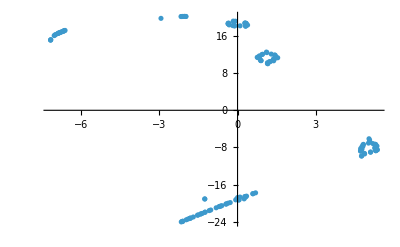

```mathematica
ListPlot[coordinatesAll]
```

```mathematica
coordinatesGen=DimensionReduce[DeleteDuplicates[allPossibleWords],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesGen;
```

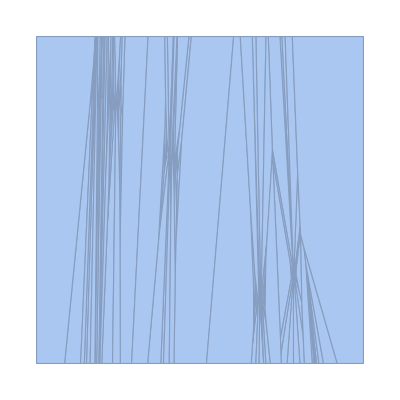

```mathematica
VoronoiMesh[coordinatesBase, AspectRatio->1]
```

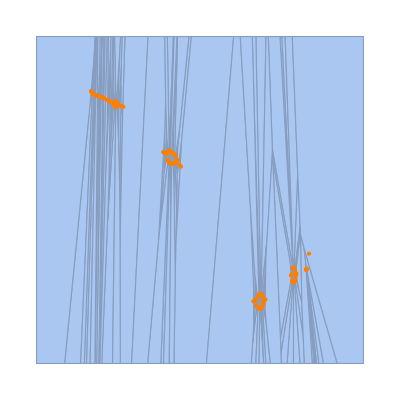

```mathematica
Show[%,Graphics[{Orange,Point[coordinatesBase]}, AspectRatio->1]]
```

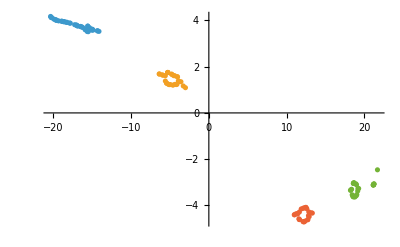

```mathematica
ListPlot[FindClusters[coordinatesBase,4,Method->"KMeans"]]
```

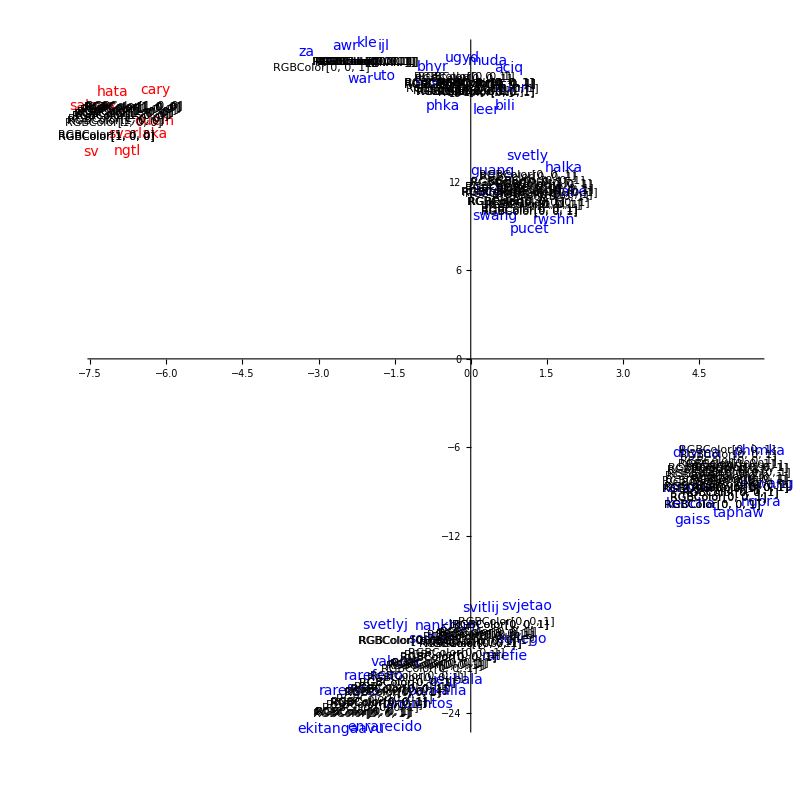

```mathematica
FeatureSpacePlot[
DeleteDuplicates[Join[
Labeled[#->Red, Style[#, Red, 14]]&/@allPossibleWords,
Labeled[#->Blue, Style[#, Blue, 14]]&/@translatedList
]],
FeatureExtractor->extractor,
LabelingSize->30,Axes->True, Method->"TSNE",ImageSize->{800,800}, AspectRatio->1
]
```

## Metrics

We have some approaches which provide us with reasonable results. However, we need to quantify and visualize our newly generated words.

```mathematica
plotFitnessHeatmap[allPossibleWords_List]:=Module[{fitnessValues,reshapedValues,size,wordsMatrix},
	  fitnessValues=fitnessFunction /@ allPossibleWords;
	  size=Ceiling[Sqrt[Length[fitnessValues]]];
	  reshapedValues=PadRight[Partition[fitnessValues,size,size,{1,1},{}],{size,size},None];
	  wordsMatrix=PadRight[Partition[allPossibleWords,size,size,{1,1},""],{size,size},None];
	  ArrayPlot[reshapedValues,ColorFunction->"TemperatureMap",Frame->True,Mesh->True,MeshStyle->Gray,
	    PlotLabel->"Fitness Heatmap: Larger is better",ColorFunctionScaling->True,
	    Epilog->Flatten[
	      Table[
	        {
	          Text[Style[wordsMatrix[[i,j]],FontSize->12,Black],{j-0.5,size-i+0.25}],
	          Text[Style[NumberForm[reshapedValues[[i,j]],{4,2}],FontSize->12,Black],{j-0.5,size-i+0.75}]
	        },
	        {i,size},{j,size}
	      ]
	    ],
	    PlotLegends->BarLegend[{"TemperatureMap",{Min[fitnessValues],Max[fitnessValues]}}]
	  ]
	]
```

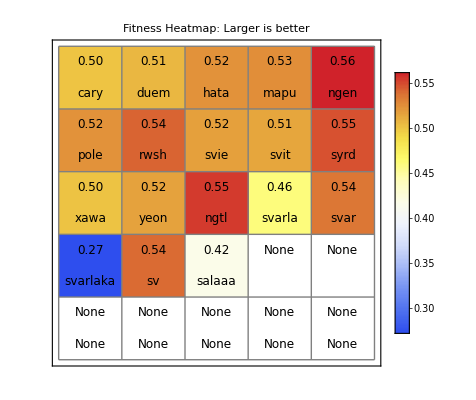

```mathematica
plotFitnessHeatmap[allPossibleWords]
```

```mathematica
WordCloud[StringTake[allPossibleWords, 1]]
```

-Graphics-

```mathematica
plotFitnessHeatmap[allPossibleWords_List]:=Module[{fitnessValues,reshapedValues,size,wordsMatrix},
	  fitnessValues=extractor /@ allPossibleWords;
	  size=Ceiling[Sqrt[Length[fitnessValues]]];
	  reshapedValues=PadRight[Partition[fitnessValues,size,size,{1,1},{}],{size,size},None];
	  wordsMatrix=PadRight[Partition[allPossibleWords,size,size,{1,1},""],{size,size},None];
	  ArrayPlot[reshapedValues,ColorFunction->"TemperatureMap",Frame->True,Mesh->True,MeshStyle->Gray,
	    PlotLabel->"Neural Net Feature Extractor Heatmap: Smaller is better",ColorFunctionScaling->True,
	    Epilog->Flatten[
	      Table[
	        {
	          Text[Style[wordsMatrix[[i,j]],FontSize->12,Black],{j-0.5,size-i+0.25}],
	          Text[Style[NumberForm[reshapedValues[[i,j]],{4,2}],FontSize->12,Black],{j-0.5,size-i+0.75}]
	        },
	        {i,size},{j,size}
	      ]
	    ],
	    PlotLegends->BarLegend[{"TemperatureMap",{Min[fitnessValues],Max[fitnessValues]}}]
	  ]
	]
```